# NG22P08. Обучение с учителем. Дельта-правило обучения

### 1. Обучающий набор

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Partition[BinaryReadList[F,"Byte",ByteOrdering->+1],Rows Cols];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]]
```

{{60000},{60000,784}}

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]]
```

{{10000},{10000,784}}

```mathematica
(*Преобразуем наборы, деля значения вектора растров на 255*)
```

```mathematica
Train=MapThread[{N[#1/225],#2}&,{Train⟦2⟧,Train⟦1⟧}];
Test=MapThread[{N[#1/225],#2}&,{Test⟦2⟧,Test⟦1⟧}];
```

### 2. Трехслойная нейрнонная сеть прямого распространения

```mathematica
test = First@Train;
```

```mathematica
(*Веса первого слоя*)
```

```mathematica
kmWeight = RandomReal[{-1,1},{10,784}];
```

```mathematica
(*2.1 Первый слой, его входы сохраняем в переменную km$X*)
```

```mathematica
kmLayer[1]:=kmWeight.(km$X=#)&
```

```mathematica
kmLayer[1][test⟦1⟧]
```

{-4.64112,-0.121064,-0.0982353,10.7665,-3.18973,5.87537,4.42532,-13.5324,0.371839,-9.68822}

```mathematica
(*2.2 Округляем значения до $MachineEpsilon, чтобы они не оказались меньше его*)
```

```mathematica
SoftMax[x_]:=With[{exp=Exp[x]},Round[exp/Total[exp],$MachineEpsilon]]
```

```mathematica
kmLayer[2]:=SoftMax
```

```mathematica
(*2.3 Оба слоя вместе*)
```

```mathematica
ClearAll[kmANN];
kmANN=RightComposition@@Array[kmLayer,2]
```

kmWeight.(km$X=#1)&/*SoftMax

```mathematica
(*Результат работы с данными весами*)
```

```mathematica
kmANN[test⟦1⟧]
```

{2.0161×10^-7,0.0000185161,0.0000189436,0.990742,8.60681×10^-7,0.00744336,0.00174589,2.7738×10^-11,0.0000303119,1.29595×10^-9}

### 3. Потери: перекрестная энтропия, дельта правило

```mathematica
RealExponent[0.,E]
```

-745.133

```mathematica
Log[0.]
```

Indeterminate

```mathematica
(*Правильный ответ будет в виде вектора, у которого на соответсвующей цифре позиции стоит 1, а в остальных позициях 0*)
```

```mathematica
UnitVector[10,9+1]
```

{0,0,0,0,0,0,0,0,0,1}

```mathematica
ClearAll[kmLoss];
kmLoss[Y_List,Digit_Integer]:=-RealExponent[Y,E].UnitVector[10,Digit+1]
```

### 4. Дельта правило обучения

```mathematica
Y = kmANN[test⟦1⟧];
YT = UnitVector[10,test⟦2⟧+1]
```

{0,0,0,0,0,1,0,0,0,0}

```mathematica
(*Градиент функции потерь*)
```

```mathematica
TensorProduct[(Y-YT),test⟦1⟧]//Dimensions
```

{10,784}

```mathematica
(*Умножая полученный градиент на скорость обучения η получаем дельта-правило. Смысл правила - мы считаем поправку к весам нейронов с какой-то скоростью*)
```

```mathematica
η TensorProduct[(YT-Y),test⟦1⟧]//Dimensions
```

{10,784}

```mathematica
(*Т.к. мы сохраняем входные данные слоя в переменную km$X, ее используем*)
```

```mathematica
ClearAll[kmTrain];
(* {Растр, Цифра} ↦ Градиент kmLoss *)
kmTrain[{X_,Digit_}]:=With[
{YT = UnitVector[10,Digit+1],Y=kmANN[X]},
TensorProduct[YT-Y,km$X]
]
(* Мини-пакет образцов ↦ ΔW без скорости обучения *)
kmTrain[miniBatch:{{_,_}..}]:=Sum[kmTrain[i],{i,miniBatch}]
```

### 5. Подбор оптимальных параметров обучения

```mathematica
(*Обучающий набор перемешивется с помощью RandomSample и его можно разделить на мини-пакеты с помощью Partition*)
```

```mathematica
(*{Сколько минибатчей, количество элементов в каждом минибатче, растр и цифра}*)
```

```mathematica
Dimensions[batch=Partition[RandomSample[Train],UpTo[10]]]
```

{6000,10,2}

```mathematica
(*Затем считается поправка весов после обработки каждого минипакета и меняем веса, умножая на скорость обучения*)
```

```mathematica
Dimensions[ΔW=kmTrain[batch⟦1⟧]]
```

{10,784}

```mathematica
(*По окончанию обработки всех минипакетов, меняем скорость обучения*)
```

```mathematica
(*Итоговая процедура для обучения*)
```

```mathematica
kmTrain[miniBatch_Integer, η0_Real,Steps_Integer, W0_List]:=Module[
{step = 0,batch, end=False},
kmWeight = W0; η=η0;
(*Проходимся циклом*)
While[ 
step≤Steps && !end, (*пока не прошли всем шагам*)
batch = Partition[RandomSample[Train],UpTo[miniBatch]]; (*Разбиваем набор на минипакеты*)
(*Проходимся по минипакетам*)
Scan[ 
(kmWeight += η kmTrain[#]; (*Считаем поправку к весам*)
step++; (*добавляем шаг*)
If[step == Steps,Return[end=True]])&, (*Если дошли до конца шагов, выходим из Scan*)
batch
];
η=0.85η; (*Уменьшаем скорость обучения*)
]
]
```

```mathematica
(*Задаем начальные веса и обучаем классификатор*)
```

```mathematica
W0=RandomReal[{-0.001,0.001},{10,784}];
```

```mathematica
Timing[kmTrain[10,0.1,1000,W0]]
```

{20.625,Null}

```mathematica
(*Карты весов*)
```

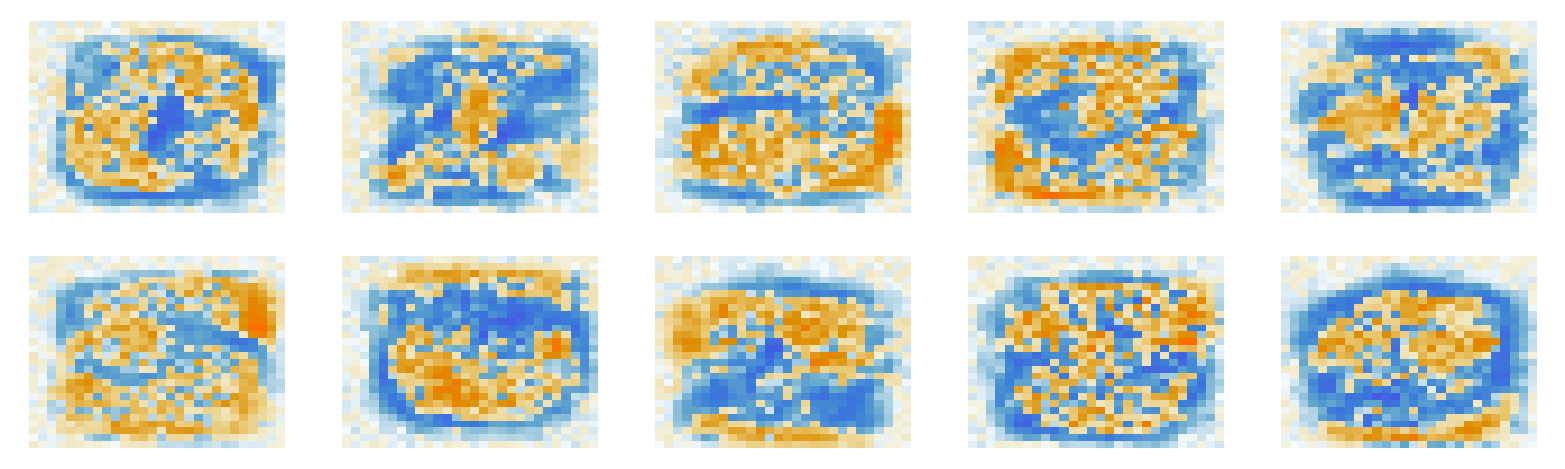

```mathematica
Partition[MatrixPlot[Partition[kmWeight⟦#⟧,28],ImageSize->Small,Frame->False]&/@Range[10],5]//Grid
```

```mathematica
(*Карты весов похожи на соответствующие им цифры, но некоторые с маленькой точностью*)
```

### 6. Качество распознавания

```mathematica
(*Тест распознавания*)
```

```mathematica
test = Test⟦1⟧;
```

```mathematica
kmANN[test⟦1⟧]//Round
```

{0,0,0,0,0,0,0,1,0,0}

```mathematica
test⟦2⟧
```

7

```mathematica
(*Списки предсказанных цифр и их сравнение с правильными *)
```

```mathematica
pred=First[TakeLargest[kmANN[#]->"Index",1]]-1&/@Test⟦;;,1⟧;
```

```mathematica
res=MapThread[(#1==#2)/.{False->0,True->1}&,{Test⟦;;,2⟧,pred}];
```

```mathematica
res=MapThread[#1==#2&,{Test⟦;;,2⟧,pred}];
```

```mathematica
(*Количество и процент неправильных распознаваний*)
```

```mathematica
Count[res,False]
```

1146

```mathematica
Count[res,False]/(Length@Test)//N//PercentForm
```

11.46%

```mathematica
(*Среднее значение функции потерь*)
```

```mathematica
Mean[kmLoss[kmANN[#⟦1⟧],#⟦2⟧]&/@Test]
```

1.57227

```mathematica
(*Неправильно распознанные растры в виде таблицы*)
```

```mathematica
iBad =Flatten[Position[res,False]];
```

```mathematica
ClearAll[kmDigits];
kmDigits[ind_List,inRow_Integer]:=Grid[Partition[Tooltip[ArrayPlot[Partition[Test⟦#,1⟧,28],ImageSize->40,Frame->False],pred⟦#⟧]&/@ind,inRow],Frame->All]
```

```mathematica
kmDigits[Take[iBad,180],20]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-